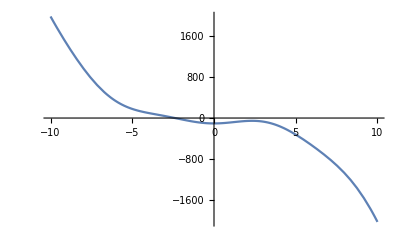

```mathematica
f[x_]:= -2 x^3- 45Cos[x]-5 12;
Plot[f[x],{x,-10,10}]
```

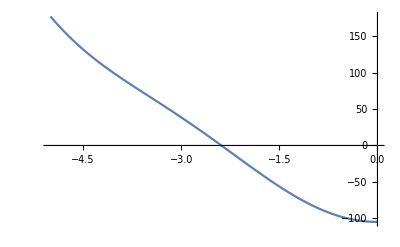

```mathematica
Plot[f[x],{x,-5,0}]
```

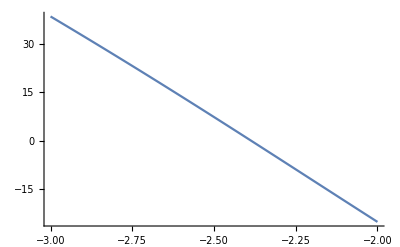

```mathematica
Plot[f[x],{x,-3,-2}]
```

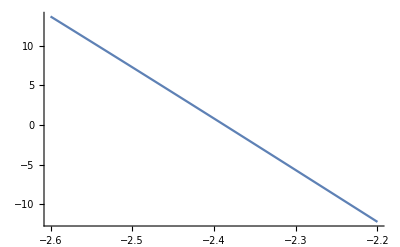

```mathematica
Plot[f[x],{x,-2.6,-2.2}]
```

```mathematica
f[-2.6]
```

f[-2.6]

```mathematica
f[-2.2]
```

f[-2.2]

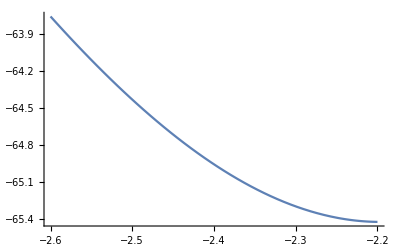

```mathematica
Plot[f'[x],{x,-2.6,-2.2}]
```

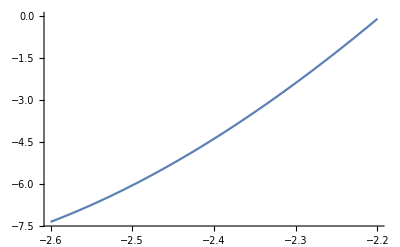

```mathematica
Plot[f''[x],{x,-2.6,-2.2}]
```

```mathematica
x0=-2.2;
p=-2.6;
```

```mathematica
f[x0]
```

f[-2.2]

```mathematica
f[p]
```

13.712

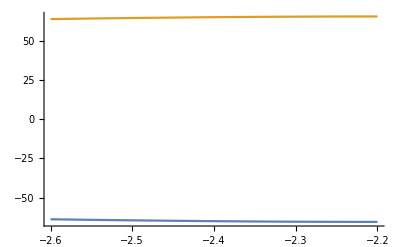

```mathematica
Plot[{f'[x],Abs[f'[x]]},{x,-2.6,-2.2}]
```

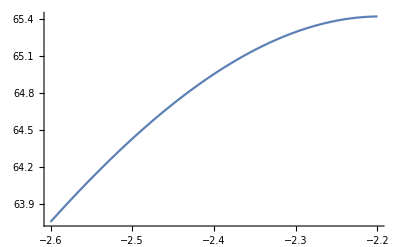

```mathematica
Plot[Abs[f'[x]],{x,-2.6,-2.2}]
```

```mathematica
Abs[f'[-2.6]]
```

63.7576

```mathematica
Abs[f'[-2.2]]
```

65.4223

```mathematica
m1 =Abs[f'[-2.6]]
M1 = Abs[f'[-2.2]]
```

63.7576

65.4223

```mathematica
CC= (M1 - m1)/m1
```

0.026111

```mathematica
(*zapochvame s iteraciite*)
```

```mathematica
x0 = -2.2;
p = -2.6;
M1 = Abs[f'[-2.2]];
m1 =Abs[f'[-2.6]];
xpred = x0;
CC = (M1 - m1)/m1;
Print["n=0: x=",x0," f(x)= ",f[x0]];
For[n=0,n<= 3,n++,
xsled = xpred - f[xpred]/(f[xpred]-f[p])(xpred-p);
eps = CC* Abs[xsled - xpred];
Print["n=",n+1," : x=",SetPrecision[xsled,12]," f(x)=",f[xsled]," eps=",eps];
xpred = xsled;
]
```

n=0: x=-2.2 f(x)= -12.2214

n=1 : x=-2.38850484957 f(x)=0.0837551 eps=0.00492206

n=2 : x=-2.38720506285 f(x)=-0.00074102 eps=0.0000339388

n=3 : x=-2.38721656204 f(x)=6.5465×10^-6 eps=3.00256×10^-7

n=4 : x=-2.38721646045 f(x)=-5.78355×10^-8 eps=2.6526×10^-9

```mathematica
(* sus stop kriteriy*)
x0 = -2.2;
p = -2.6;
M1 = Abs[f'[-2.2]];
m1 =Abs[f'[-2.6]];
xpred = x0;
CC = (M1 - m1)/m1;
Print["n=0: x=",x0," f(x)= ",f[x0]];
epsusl = 10^(-5);
eps = 1;
For[n=0,eps >= epsusl,n++,
xsled = xpred - f[xpred]/(f[xpred]-f[p])(xpred-p);
eps = CC* Abs[xsled - xpred];
Print["n=",n+1," : x=",SetPrecision[xsled,12]," f(x)=",f[xsled]," eps=",eps];
xpred = xsled;
]
```

n=0: x=-2.2 f(x)= -12.2214

n=1 : x=-2.38850484957 f(x)=0.0837551 eps=0.00492206

n=2 : x=-2.38720506285 f(x)=-0.00074102 eps=0.0000339388

n=3 : x=-2.38721656204 f(x)=6.5465×10^-6 eps=3.00256×10^-7

```mathematica
Log2[(-2.2-(-2.6))/10^(-5)]-1
```

14.2877

```mathematica
A = ({{-1/8, 1/10, 0, 6}, {-0.02, 1+1/8, 0.2, 5}, {-0.01, 0.2, 1+1/9, 7}});
n = Length[A];

For[
col = 1 , col <= n, col++,
A[[col]]=A[[col]]/A[[col,col]];
For[row = 1 , row <= n , row++,
If[row != col,A[[row]] = A[[row]] - A[[row,col]] * A[[col]]]
];
Print[A // MatrixForm]
]
```

(1 | -4/5 | 0 | -48
0. | 1.109 | 0.2 | 4.04
0. | 0.192 | 1.11111 | 6.52)

(1. | 0. | 0.144274 | -45.0857
0. | 1. | 0.180343 | 3.64292
0. | 0. | 1.07649 | 5.82056)

(1. | 0. | 0. | -45.8658
0. | 1. | 0. | 2.66781
0. | 0. | 1. | 5.407)

```mathematica
A = ({{-1/8, 0.1, 0, 6}, {-0.02, 1+1/8, 0.2, 5}, {-0.01, 0.2, 1+1/9, 7}});
n = Length[A];
deter = 1;
For[
col = 1 , col <= n, col++,
deter = deter * A[[col,col]];

A[[col]]=A[[col]]/A[[col,col]];
For[row = 1 , row <= n , row++,
If[row != col,A[[row]] = A[[row]] - A[[row,col]] * A[[col]]]
];
Print[A // MatrixForm]
]
Print["Детерминантата на матрицата е ",deter]
```

(1 | -0.8 | 0 | -48
0. | 1.109 | 0.2 | 4.04
0. | 0.192 | 1.11111 | 6.52)

(1. | 0. | 0.144274 | -45.0857
0. | 1. | 0.180343 | 3.64292
0. | 0. | 1.07649 | 5.82056)

(1. | 0. | 0. | -45.8658
0. | 1. | 0. | 2.66781
0. | 0. | 1. | 5.407)

Детерминантата на матрицата е -0.149228

```mathematica
Det[({{-1/8, 0.1, 0}, {-0.02, 1+1/8, 0.2}, {-0.01, 0.2, 1+1/9}})]
```

-0.149228

```mathematica
A = ({{-1/8, 0.1, 0, 1, 0, 0}, {-0.02, 1+1/8, 0.2, 0, 1, 0}, {-0.01, 0.2, 1+1/9, 0, 0, 1}});
n = Length[A];
deter = 1;
For[
col = 1 , col <= n, col++,(*цикъл по стъпките*)
deter = deter * A[[col,col]];
(*първи етап-получаваме единицата на мястото на главния елемент*)
A[[col]]=A[[col]]/A[[col,col]];
(*втори етап-получаване на нули във всички останали елементи от стълба*)
For[row = 1 , row <= n , row++,
If[row != col,A[[row]] = A[[row]] - A[[row,col]] * A[[col]]]
];
Print[A // MatrixForm]
]
```

(1 | -0.8 | 0 | -8 | 0 | 0
0. | 1.109 | 0.2 | -0.16 | 1. | 0.
0. | 0.192 | 1.11111 | -0.08 | 0. | 1.)

(1. | 0. | 0.144274 | -8.11542 | 0.721371 | 0.
0. | 1. | 0.180343 | -0.144274 | 0.901713 | 0.
0. | 0. | 1.07649 | -0.0522994 | -0.173129 | 1.)

(1. | 0. | 0. | -8.10841 | 0.744574 | -0.134023
0. | 1. | 0. | -0.135512 | 0.930717 | -0.167529
0. | 0. | 1. | -0.0485834 | -0.160828 | 0.928949)